```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
dat=Import["infoseq_15.csv"]
```

{{9,0.00714047},{67,0.0127164},{13,0.0179127},{16,0.0227846},{17,0.0294803},{59,0.0361631},{70,0.0497722},{39,0.0759585},{43,0.120456},{89,0.19676},{93,0.30768},{55,0.458223},{76,0.646054},{22,0.850405},{66,1.0488}}

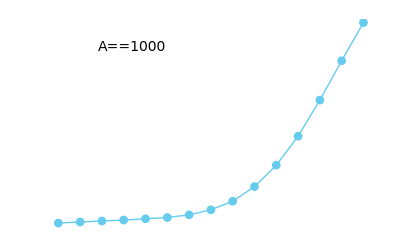

```mathematica
ListPlot[dat[[;;,2]],Axes->None,Frame->Auto,FrameLabel->{{"mutual info",None},{genes,None}},FrameTicks->{Auto,{T@{Range[1,Length@dat],Style[#,12]&/@dat[[;;,1]]},Auto}},ImageSize->a5rsize,Joined->True,PlotMarkers->Auto,Epilog->Text[Style[A==10^3,14],Scaled[{0.3,0.9}],{0.3,0.9}]]
```

```mathematica
expdf["testpr",%]
```

testpr.pdf